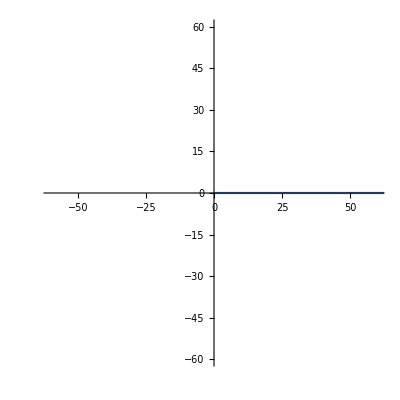
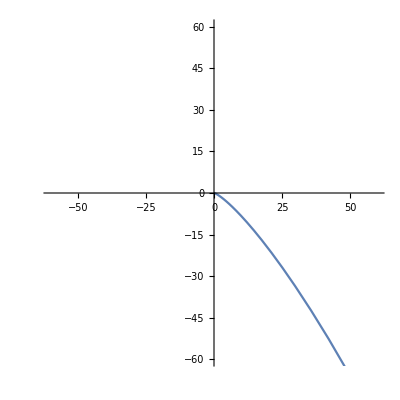
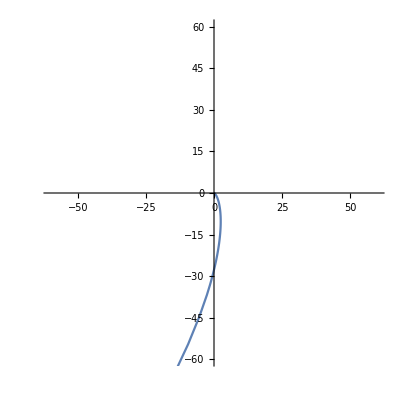
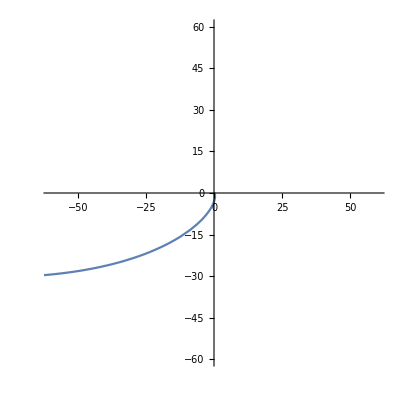
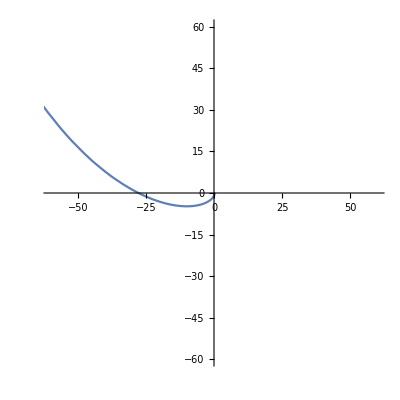
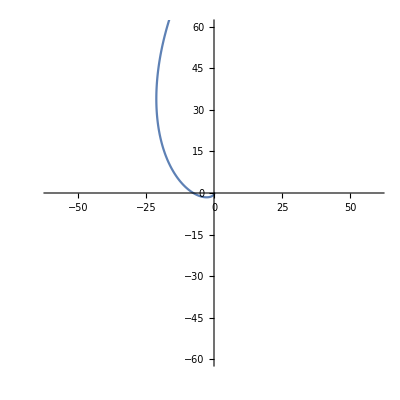
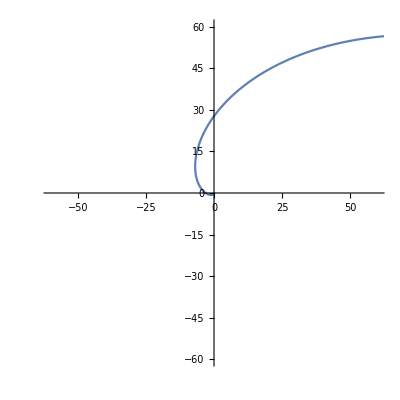
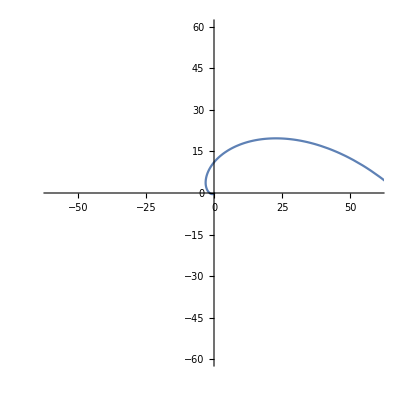

```mathematica
gif = Table[ParametricPlot[{Re[g[t]*f[t,fr]],Im[g[t]*f[t,fr]]},{t,0,4},PlotRange->{-60,60}],{fr,0,3,0.05}]
```

```mathematica
Export["goldenRatio FourierTransformation.gif",Flatten[{gif,Table[gif[[i]],{i,Length[gif]-1,2,-1}]}]]
```

goldenRatio FourierTransformation.gif

```mathematica
SystemOpen["goldenRatio FourierTransformation.gif"]
```